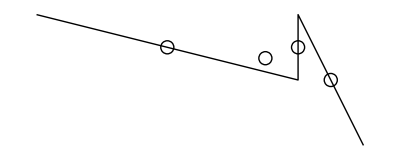

```mathematica
x1=10;x2=50;x3=50;x4=60;
y1=50;y2=40;y3=50;y4=30;
Graphics[{
Line[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}],
Circle[{x1+(x2-x1)/2,y1+(y2-y1)/2},1],
Circle[{x2+(x3-x2)/2,y2+(y3-y2)/2},1],
Circle[{x3+(x4-x3)/2,y3+(y4-y3)/2},1],
Circle[{((x1+(x2-x1)/2)+(x2+(x3-x2)/2)+(x3+(x4-x3)/2))/3,((y1+(y2-y1)/2)+(y2+(y3-y2)/2)+(y3+(y4-y3)/2))/3},1]
}]
```

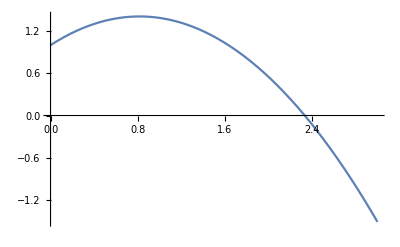

```mathematica
g=-9.8;
θ=45°;
v0=4;
yi=1;
y[x_]:=yi+x Tan[θ]+1/2(g x^2)/(v0 Cos[θ])^2;

Plot[y[x],{x,0,3}]
```

```mathematica
Solve[{
10==yi+v0*Sin[θ]*x/(v0*Cos[θ])+1/2 g (x/(v0*Cos[θ]))^2}]
t==x/(v0*Cos[θ])
```

{{x→0.816327-3.74533 ⅈ},{x→0.816327+3.74533 ⅈ}}

t==x/(2 √2)

```mathematica
Clear["Global`*"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.264631,v0→189.149,θ→0.0468287},{t→1.54238,v0→33.6048,θ→0.266633}}

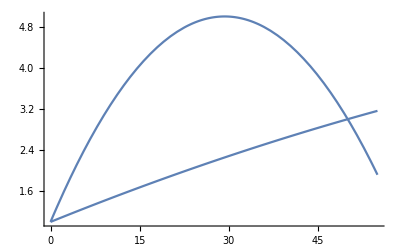

```mathematica
y=5;
a=-9.8;
x=50;
vf=0;
yi=1;
yf=3;
sol=Solve[{
t==x/(v0*Cos[θ]),
vf^2==(Sin[θ]v0 )^2+2 a (y-yi),
yf==yi+Sin[θ]v0  t+1/2 a t^2,t>0,v0>0},{t,v0,θ}]/.C[1]->0
Y[X_]:=yi+X Tan[θ]+1/2(a X^2)/(v0 Cos[θ])^2/.sol
Plot[Y[X],{X,0,55}]
```

```mathematica
g=-9.8;
θ=45°;
v0=4;
yi=1;
```